```mathematica
Subscript[R, c]= 1;
```

```mathematica
backgroundsolution[ϕ0_]:= Module[
{startI = 0.000001,
endI = 1.001,
startE = .99,
endE = 1000,
Λ = 1,
ϕcosmological = .001,
ρ = 10},
backgroundsolutioninterior= NDSolve[{1/Subscript[R, c] D[ϕ[r],r,r]+2/(r Subscript[R, c])D[ϕ[r],r]+2/Λ^2(4/(r Subscript[R, c])D[ϕ[r],r]+ 2/(r^2 Subscript[R, c]^2)(D[ϕ[r],r])^2)==8π ρ,ϕ'[startI] ==0,ϕ[startI] ==  ϕ0},
ϕ,{r,startI,endI}];
backgroundsolutionexterior=NDSolve[{1/Subscript[R, c]^2 D[ϕe[r],r,r]+2/(r Subscript[R, c])D[ϕe[r],r]+2/Λ^2(4/(r Subscript[R, c])D[ϕe[r],r]+ 2/(r^2 Subscript[R, c]^2)(D[ϕe[r],r])^2)==0,ϕe[startE] ==  ϕ[1]/.backgroundsolutioninterior,ϕe'[startE] == ϕ'[1]/.backgroundsolutioninterior},
ϕe,{r,startE,endE}];
Proximity= (ϕe[endE]/.backgroundsolutionexterior) -ϕcosmological;
Prepend[Proximity,ϕ0]]
```

```mathematica
Trialend = .1;
Trialstart = 0;
Trialstep = .001;
(*solutions = Table[Proximity[i], {i, Trialstart, Trialend, Trialstep}];*)
```

```mathematica
Solutions = Map[backgroundsolution,Range[Trialstart,Trialend,Trialstep]];
```

```mathematica
(*Solutions = Parallelize[Map[backgroundsolution,Range[Trialstart,Trialend,Trialstep]]];*)
```

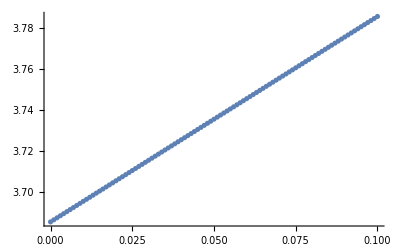

```mathematica
ListPlot[Solutions]
```